### Figure 3.2

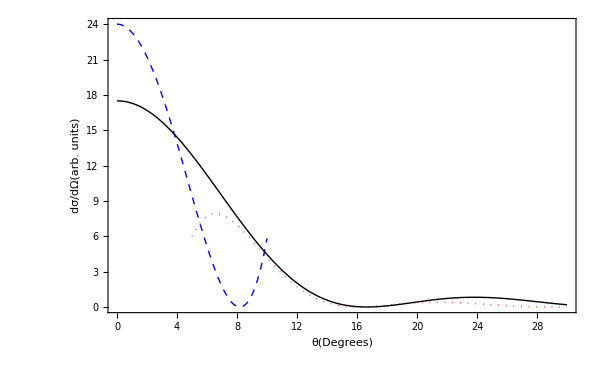

fig3_2.png

```mathematica
R=7;
k=2;
scale=1/100;
fs=25;
dσ1=scale*(2R)/(π*k*(θ*Degree)^2*Sin[θ*Degree])Cos[k*R*θ*Degree+π/4]^2;
dσ2=scale*(k^2 R^4)/4(1-(k*R*θ*Degree/2)^2)^2;
dσ3=scale*1750*Sinc[k*5.4*θ*Degree]^2;
p1=Plot[dσ1,{θ,5,30},PlotRange->All,PlotStyle->{Red,Dotted,Thick}];
p2=Plot[dσ2,{θ,0,10},PlotRange->All,PlotStyle->{Blue,Dashed,Thick}];
p3=Plot[dσ3,{θ,0,30},PlotRange->All,PlotStyle->{Black,Thick}];
final=Show[p1,p2,p3,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"θ(Degrees)","dσ/dΩ(arb. units)"},LabelStyle->{fs,Black},ImageSize->600]
SetDirectory[NotebookDirectory[]];
Export["fig3_2.png",final]
```

```mathematica
Directory[]
```

/home/clpetrie

### Woods-Saxon shape

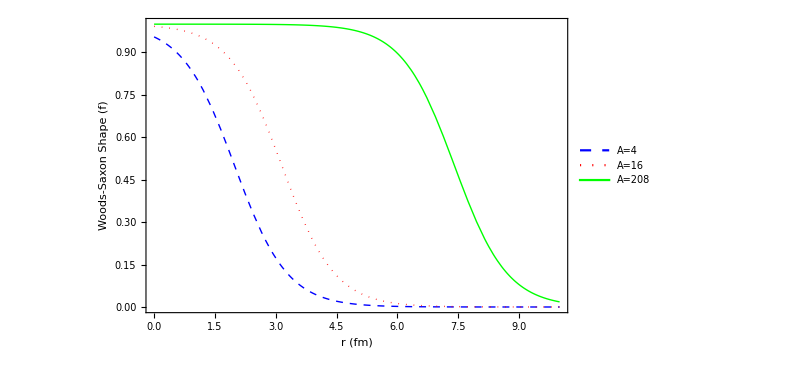

woodssaxon.png

```mathematica
f[x_]:=(1+Exp[x])^-1;
r0=1.25(*fm*);
aU=0.65(*fm*);

As={4,16,208};
fs=25;
plot=Plot[{f[(r-r0*A^(1/3))/aU]/.A->As[[1]],f[(r-r0*A^(1/3))/aU]/.A->As[[2]],f[(r-r0*A^(1/3))/aU]/.A->As[[3]]},{r,0,10},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"r (fm)","Woods-Saxon Shape (f)"},LabelStyle->{fs,Black},ImageSize->600,PlotStyle->{{Blue,Dashed,Thick},{Dotted,Red,Thick},{Green,Thick}},PlotLegends->Placed[{Style[StringJoin["A=",ToString[As[[1]]]],fs],Style[StringJoin["A=",ToString[As[[2]]]],fs],Style[StringJoin["A=",ToString[As[[3]]]],fs]},{0.85,0.8}]]
SetDirectory[NotebookDirectory[]];
Export["woodssaxon.png",plot]
```

### Figure 3.3

```mathematica
Clear["`*"]
```

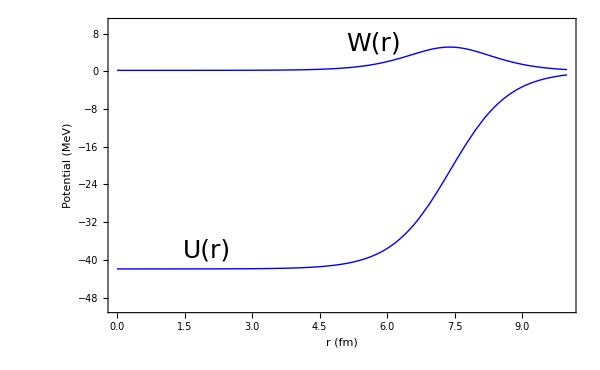

fig3_3.png

```mathematica
fs=25;
f[x_]:=(1+Exp[x])^-1;
r0=1.25(*fm*);
aU=0.65(*fm*);
aW=0.47(*fm*);
W0=Max[0.22*ϵ-2,0];
W1=Max[12-0.25*ϵ+24*t3(NN-Z)/A,0];
U0=-50-48*t3(NN-Z)/A+0.3*ϵ;
rep={NN->126,Z->82,A->208,ϵ->10,t3->-0.5};
U[r]=U0*f[(r-r0*A^(1/3))/aU]/.rep;
W[r]=W0*f[(r-r0*A^(1/3))/aU]-4*W1*aW*D[f[(r-r0*A^(1/3))/aU],r]/.rep;

p1=Plot[Evaluate[U[r]/.rep],{r,0,10},PlotRange->{{0,10},{-50,10}},PlotStyle->{Blue,Thick}];
p2=Plot[Evaluate[W[r]/.rep],{r,0,10},PlotStyle->{Blue,Thick}];
plot=Show[p1,p2,Frame->{{True,False},{True,False}},FrameLabel->{"r (fm)","Potential (MeV)"},LabelStyle->{fs,Black},ImageSize->600,Epilog->{Text[Style["W(r)",fs],{5.7,6}],Text[Style["U(r)",fs],{2,-38}]}]
SetDirectory[NotebookDirectory[]];
Export["fig3_3.png",plot]
```